1/(√(1-b^2))

(-1+1/(√(1-b^2)))/(√(1-b^2))

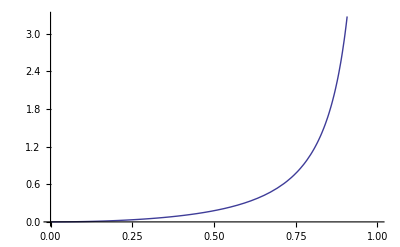

```mathematica
g=1/Sqrt[1-b^2]
it0=g*(g-1)
Plot[it0,{b,0,1}]
```

```mathematica
f=g*b
it=(f^4+f^2)/(g^2+g)
Plot[it,{b,0,1}]
```

b/(√(1-b^2))

(b^4/((1-b^2)^2)+b^2/(1-b^2))/(1/(1-b^2)+1/(√(1-b^2)))

-Graphics-

```mathematica
FullSimplify[it0-it,{b>0}]
```

0

```mathematica
Series[it,{b,0,2}]
```

b^2/2+O[b]^3